# Examining Stock Pricing “Anomalies”

Jonathan Zhou
Mentor : Dr. Phil Maymin

Stock markets are volatile environments in which there is wild fluctuation. This project explores the notion of “anomaly” within the market. Stock returns for the Dow Jones Industrial Average and its components are aggregated as a function of time. This signal is transformed into an anomaly curve by utilizing previous time points to examine the probability that a current time point arose from the distribution of prior time points (estimated by kernel density estimate). The stability and fidelity of this method of anomaly detection was assessed via comparisons to baselines. Statistical analysis and visualization were performed to assess the relation of volatility and return on anomaly as well as inter-anomaly correlation. The notion of systemic anomaly is also explored.

## Initialization and Global Parameters

Let us begin by defining some parameters for this study

Financial Entities of Interest
We will examine the Dow Jones Industrial Average and its components

```mathematica
FEOI=Join[{Entity["Financial","^DJI"]},EntityList[EntityClass["Financial","DowJonesIndustrialAverageComponents"]]]
```

{Dow Jones Industrial Average,3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,DowDuPont Inc,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

Examined time interval prior to present

```mathematica
ΔStockT=Quantity[2, "Years"];
```

Anomaly Window Size

```mathematica
windowSize=21;(* Business Days*)
```

Anomaly Training Days per window

```mathematica
APDW =20;(*Business Days*)
```

## Section I: Data Aggregation

In the Wolfram Language, financial data is encapsulated in financial entities

```mathematica
Entity["Financial","^DJI"][EntityProperty["Financial","Last"]]
```

{Day: Tue 9 Jul 2019,26783.5}

```mathematica
Entity["Financial","^DJI"][EntityProperty["Financial","Return"]]
```

-1.11022×10^-14 %

### Acquire Stock Data

getStockTS is defined to retrieve the returns for stocks for a certain financial entity for a defined time period

```mathematica
getStockTS[finEnt_,timeint_Quantity]:=
   finEnt[EntityProperty["Financial","Return",
   {"Date"->Interval[{Today-timeint,Today}]}]]
```

Here is a plot of Dow Jones returns over the past two years

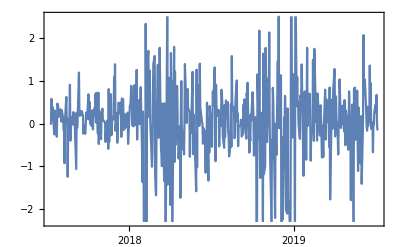

```mathematica
getStockTS[Entity["Financial","^DJI"],Quantity[2, "Years"]]//DateListPlot
```

stockTs stores the entities with their timeseries

```mathematica
stockTs = AssociationMap[getStockTS[#,ΔStockT]&,FEOI];
```

DuPont de Nemours is interesting because it was formed by the merger of Dow Chemical and DuPont on August 31, 2017. However, this means that there is only a limited amount of stock data for it and so it will be removed.

```mathematica
stockTs = KeyDrop[stockTs,{Entity["Financial","NYSE:DWDP"]}];
```

```mathematica
FEOI =FEOI/.Entity["Financial","NYSE:DWDP"]->Nothing;
```

Save the stock data

```mathematica
DumpSave["stockReturns2YTs.mx",stockTs];
```

Here are plots of all stock returns over the past two years

```mathematica
Manipulate[stockTs[entity]//DateListPlot,{entity,FEOI},SaveDefinitions->True]
```

Here is a pre-prepared version of the stock data

```mathematica
stockTs=;
```

## Section II: An Exploration of “Anomaly”

In this step, anomaly will be defined and the return percentages will be converged into a probability of anomaly.

### Anomaly detection with Kernel Density Estimation

Although the wolfram language provides a simple function for anomaly detection, it does not offer interpretability in terms of the inner workings of the function and so I elected to use a relatively similar but more transparent method of anomaly detection, which is quite similar to the built in anomaly detection.

In this section, “anomalous” is defined as  the probability for a distribution of prior timeseries values converted into a Kernel Density Estimate distribution generate a sample that has a lower PDF than the sample in question (RarerProbability). In essence, RarerProbability is a multivariate extension of “two-tailed” p-value.

#### A visual demonstration of anomaly detection via RarerProbability and KDE in LearnDistrobution

Suppose we have random variable  x and we wish to identify if point z would be considered anomalous under x. The first step would be to consider the distribution of points x.

Let us declare some points from x

```mathematica
x = {5,5,5,4,4,6,3,14,14,14,13,13,12,11,15,15};
```

The distribution  of x can be empirically “learned”/estimated through a kernel density estimation, which smooths out the points by superimposing kernels of certain bandwidths about each point to ultimately create an estimate of the PDF of the random variate. 

Formally, the  PDF for the KDE using a gaussian kernel of x is given by 1/(m h)∑_(i=1)^m k((x-x_i)/h) with gaussian kernel function k=1/(√(2π))ⅇ^(-u^2/(2 h^2)), kernel size h and a number of training examples m.

Let us fit a KDE to x

```mathematica
ld = LearnDistribution[x,Method->"KernelDensityEstimation",FeatureExtractor->"Minimal"]
```

LearnedDistribution[…]

Let’s plot the PDF of the KDE

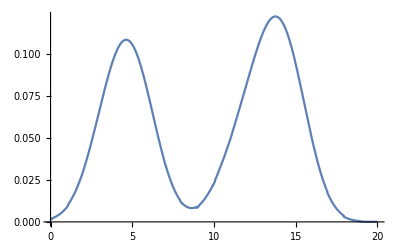

```mathematica
Plot[PDF[ld,x],{x,0,20}]
```

Suppose that I wish to determine whether the points 9, 25, 13, and 5 are anomalous or not

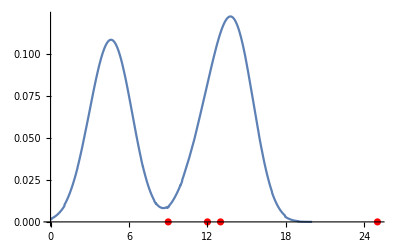

```mathematica
Show[Plot[PDF[ld,x],{x,0,20}],ListPlot[{{9,0},{25,0},{12,0},{13,0}},PlotStyle->Red],PlotRange->All]
```

Here are the assigned scores for anomaly

```mathematica
#->1- RarerProbability[ld,#]&/@{9,25,13,5}//Column
```

9→0.996937
25→1.
13→0.217346
5→0.33698

Here is a plot of anomaly probability with the PDF of the KDE

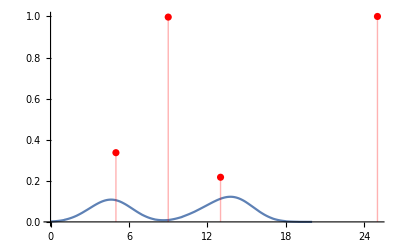

```mathematica
Show[Plot[PDF[ld,x],{x,0,20}],ListPlot[{#,1- RarerProbability[ld,#]}&/@{9,25,13,5},PlotStyle->Red,Filling->Axis],PlotRange->All]
```

#### Anomaly detection for timeseries

tsw2AnomalProb outputs anomaly probabilities (utilizing KDE as the method of distribution estimation) within a certain time series window

ts denotes the timeseries

t denotes the amount of training data

an denotes the period audited by anomaly detection

Rarer probabilities denotes the probability to generate a sample with lower PDF than data (tending towards zero is more anomalous)

```mathematica
tsw2AnomalProb[ts_,t_]:=
  Module[{tr,an,ad},
{tr,an}= TakeDrop[ts,t];
SeedRandom[0];
ad = LearnDistribution[tr,RandomSeeding->0,Method->"KernelDensityEstimation",
					   TimeGoal->1,TrainingProgressReporting->None];
1-RarerProbability[ad,an] (* Higher quantities are more anomalous*)
]
```

Here is example usage of tsw2Anomal Prob

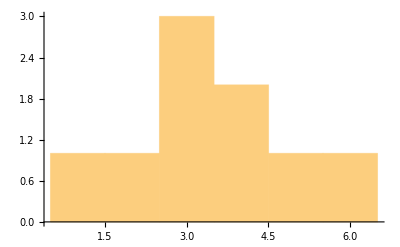

```mathematica
(λ ={3,3,3,2,4,5,1,6,4,4,8})//Histogram[Drop[#,-2],{1}]&
```

```mathematica
tsw2AnomalProb[λ,9]
```

{0.264663,0.974603}

Note that the anomaly score assigned to 4 (0.2473) is much lower than assigned to 8 (.970821)

#### (Non)-Determinism in Built-in Functions

Unfortunately, throughout the development of the anomaly detection routines, it was discovered that there was some difficultly in controlling the output of AnomalyDetection

Originally, I had intended to use Wolfram Language's builtin "AnomalyDetection” function essentially as a moving window kernel which I apply across the time series.

```mathematica
tsw2AnomalProbOrig[ts_,t_]:=
   Module[{tr,an},
     {tr,an}= TakeDrop[ts,t];
     {AnomalyDetection[tr,Method->"KernelDensityEstimation",
                          RandomSeeding-> 0,
                          PerformanceGoal->"Quality",
                          TrainingProgressReporting->"SimplePanel"],
                          an}
]
```

However, I ultimately decided against simply using Anomaly Detection because of its black box nature, as well as the difficultly in properly controlling the parameters of the model as demonstrated by the problems with RarerProbabiliy and LearnDistribution below.

#### A Demonstration of Non-Determinism in LearnDistrobution and a bug with PDF

An interesting problem which I came across with regards to RarerProbability was that the function did not always have a deterministic output.

Here is a sample of values from the Dow Jones stock returns:

```mathematica
testValues =
```

{-0.00027178,0.0000256907,0.0057485,0.000972964,0.00392751,-0.000370649,-0.00254234,0.00306006,-0.00133868,-0.00146726,-0.00310008,0.0046604,0.00451479,0.00393994,0.00154887,0.00278558,0.00332555,0.00238209,0.000447851,0.00302868}

Let us learn the distribution of testValues twice, and set the random seeds

```mathematica
SeedRandom[0];
testLd = Table[LearnDistribution[Normal[testValues],RandomSeeding->0,FeatureExtractor->"Minimal",Method->"KernelDensityEstimation"],2]
```

{LearnedDistribution[…],LearnedDistribution[…]}

Notice that the RarerProbabilities for the exact same numbers are in fact different

```mathematica
RarerProbability[testLd⟦1⟧,{-.001,10^-4,0}]
```

{0.714697,0.841741,0.875572}

```mathematica
RarerProbability[testLd⟦2⟧,{-.001,10^-4,0}]
```

{0.626831,0.755677,0.81626}

Here’s another interesting phenomenon I found. PDF should not be greater than 1, and the quantities are exactly the same for both distributions.

```mathematica
PDF[testLd⟦1⟧,{-.001,10^-4,0}]
```

{117.197,122.492,123.293}

```mathematica
PDF[testLd⟦2⟧,{-.001,10^-4,0}]
```

{117.197,122.492,123.293}

In conclusion, there are problems within both LearnDistribution and RarerProbability. It seems that either RarerProbability is non-deterministic or that the random seed doesn’t properly control LearnDistribution.

#### An Empirical Demonstration of Relative “Stability”

Although I encountered these issues with non-determinism, I found the process was stable enough to perform analysis on and detected valid points of anomaly. Here I provide an empirical demonstration of relative stability

Let us generate four samples of anomaly detection upon the Dow Jones Industrial Average

```mathematica
testingDowTs2AnomalProb = Table[ts2AnomalProb[stockTs[Entity["Financial","^DJI"]],APDW,windowSize],4]
```

```mathematica
{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}
```

Here’s a pre-prepared version of the prior data

```mathematica
testingDowTs2AnomalProb  = ;
```

Here’s a histogram of anomaly distribution

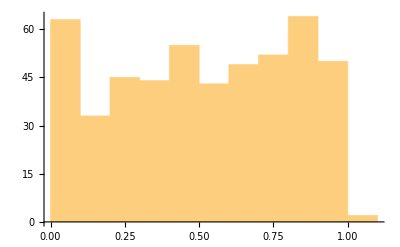
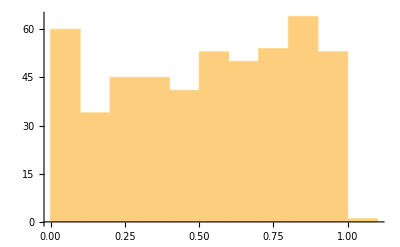
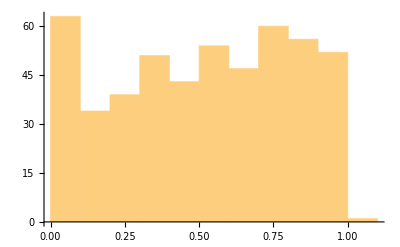
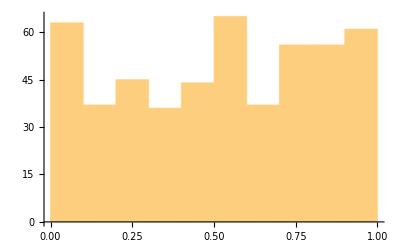

```mathematica
Histogram/@testingDowTs2AnomalProb
```

Here’s the list plots of anomaly probability across time

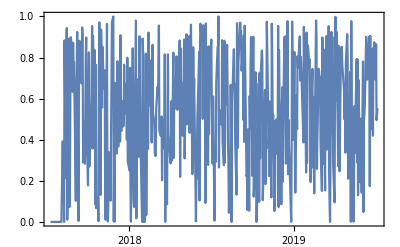
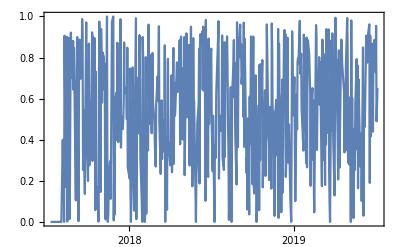
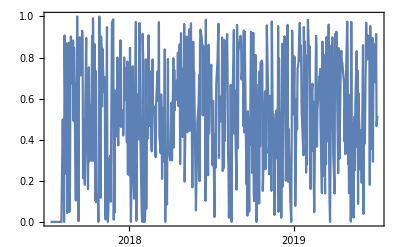
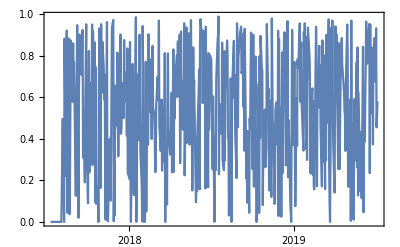

```mathematica
DateListPlot/@testingDowTs2AnomalProb
```

Here’s the anomalies as color upon the time series of returns

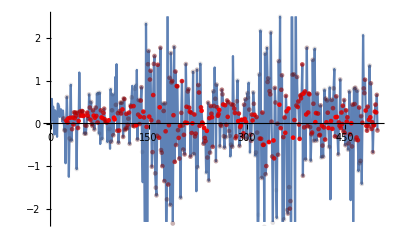
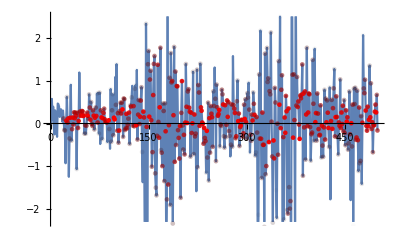
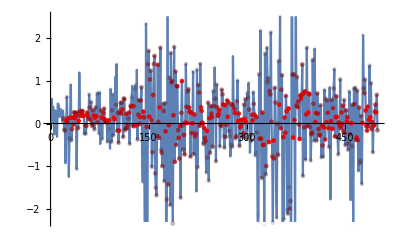
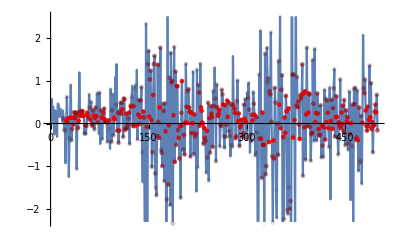

```mathematica
Table[ListLinePlot[mergeOnColor[stockTs[Entity["Financial","^DJI"]],testingDowTs2AnomalProb⟦x⟧]],{x,4}]
```

Here’s the Pearson Correlation between the output values

```mathematica
Correlation[Transpose[#["Values"]&/@testingDowTs2AnomalProb]]//MatrixForm
```

(1. | 0.979797 | 0.979987 | 0.980295
0.979797 | 1. | 0.980111 | 0.979423
0.979987 | 0.980111 | 1. | 0.981377
0.980295 | 0.979423 | 0.981377 | 1.)

Here’s a scatter plot of the values against each other

```mathematica
Manipulate[ListPlot[Transpose[{testingDowTs2AnomalProb⟦ψ⟧["Values"],testingDowTs2AnomalProb⟦ϵ⟧["Values"]}]],{{ψ,1},1,4,1},{{ϵ,2},1,4,1},SaveDefinitions->True]
```

These demonstrations indicate that although the anomaly detection is ultimately non-deterministic, the signal exists and points which are “anomalous” are being detected in a consistent manner.

### Comparison of KDE and Normal Distributions for Anomaly Detection (Why the Use of KDE)

Another thing I would like to demonstrate is that the method of “learning” distribution via KDE is better than a simple test based on a normal  distribution.

Here I describe a procedure by which utilizes normal distribution instead of a Kernel density estimate in order to derive a Rarer Probability

Fit a standard distribution to the data

```mathematica
getNormalDistribution[ts_]:=NormalDistribution[Mean[ts]//N,StandardDeviation[ts]//N]
```

Here’s an example of getting a fitted normal distribution

```mathematica
getNormalDistribution[{1,2,3,4,5}]
```

NormalDistribution[3.,1.58114]

```mathematica
tsw2AnomalProbNormDist[ts_,t_]:=
	Module[{tr,an,ad},
		{tr,an}= TakeDrop[ts,t]//N;
		SeedRandom[0];
		ad = getNormalDistribution[tr];
		RarerProbability[ad,an//N]//N
]
```

```mathematica
ts2AnomalProbNormDist[ts_,t_,window_]:=
	Module[{out},
		out=tsw2AnomalProbNormDist[#,t]&/@(Partition[ts["Values"],window,window-t]//N)//Flatten;
	TimeSeries[Transpose[{ts["Dates"],PadLeft[out,ts["PathLength"]]}]]
]
```

Let us generate the anomaly time series based on the normal distribution

```mathematica
tstNormDistDow = ts2AnomalProbNormDist[stockTs[Entity["Financial","^DJI"]],APDW,windowSize]
```

TimeSeries[…]

Here are pre-computed values

```mathematica
tstNormDistDow=TimeSeries[…]
```

TimeSeries[…]

Here is the correlation matrix between the normal values and the four trial runs on the Dow Jones using KDE with the normal distribution values being the first row/column. Note the substantial difference between the values in the first row/column and those in the rest of the matrix.

```mathematica
Correlation[Transpose[Join[{tstNormDistDow["Values"]},#["Values"]&/@testingDowTs2AnomalProb]]]//MatrixForm
```

(1. | 0.897741 | 0.899544 | 0.896152 | 0.892753
0.897741 | 1. | 0.979797 | 0.979987 | 0.980295
0.899544 | 0.979797 | 1. | 0.980111 | 0.979423
0.896152 | 0.979987 | 0.980111 | 1. | 0.981377
0.892753 | 0.980295 | 0.979423 | 0.981377 | 1.)

Here is a scatter plot between the normal anomaly probabilities and the KDE values.

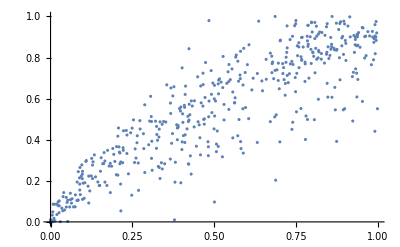

```mathematica
ListPlot[Transpose[{tstNormDistDow["Values"],testingDowTs2AnomalProb⟦1⟧["Values"]}]]
```

### Applying Anomaly Detection Across a Timeseries

The previously defined time series to anomaly probability only operate on a window of a time series, in order to convert entire time series, this function must be applied over each sub-window of the time series, starting at the beginning and moving over one each time.

ts2AnomalProb converts an entire timeseries into a timeseries of anomaly probability

ts denotes the timeseries

t denotes the period of prediction

window denotes the size of the window for anomaly detect

|window-lookahead|lookahead|
|          window          |

```mathematica
ts2AnomalProb[ts_,t_,window_]:=
   Module[{out},
     Print["abc called ts2AnomalProb"];
     out = tsw2AnomalProb[#,t]&/@Partition[ts["Values"],window,window-t]//Flatten;
     TimeSeries[Transpose[{ts["Dates"],PadLeft[out,ts["PathLength"]]}]]
   ]
```

### Creating Anomaly Timeseries for all Relevant Stocks

Applying the conversion from return to anomaly probability across the stock timeseries association

```mathematica
anomalTs = ts2AnomalProb[#,APDW,windowSize]&/@stockTs
```

```mathematica
<|Entity["Financial","NYSE:MMM"]->TimeSeries[…],Entity["Financial","NYSE:AXP"]->TimeSeries[…],|>
```

Here is a pre-prepared version of the anomaly timeseries

```mathematica
anomalTs=;
```

## Section III: Examination of Anomalous Points through Visualization

### Color Plot

mergeOnColor is a function to join two timeseries into one where one of the timeseries is encoded into color

```mathematica
mergeOnColor[ts_,colorTs_]:= Style@@@Transpose[{ts["Values"],
                             Blend[{Transparent,Red},#]&/@colorTs["Values"]}]
```

For example, here is the combination of the Dow Jones and it’s anomaly probability

```mathematica
mergeOnColor[stockTs[Entity["Financial","^DJI"]],anomalTs[Entity["Financial","^DJI"]]]//Take[#,30]&
```

{0.00256907 %,0.57485 %,0.0972964 %,0.392751 %,-0.0370649 %,-0.254234 %,0.306006 %,-0.133868 %,-0.146726 %,-0.310008 %,0.46604 %,0.451479 %,0.393994 %,0.154887 %,0.278558 %,0.332555 %,0.238209 %,0.0447851 %,0.302868 %,0.11592 %,-0.149559 %,-0.165902 %,-0.928354 %,0.0655099 %,0.619398 %,0.0240069 %,0.117642 %,-1.24468 %,-0.350425 %,0.134905 %}

Here is the  anomaly probability for all examined stocks

```mathematica
Manipulate[DateListPlot[anomalTs[entity],ImageSize->Large],{entity,FEOI},SaveDefinitions->True]
```

This is the combination of the previous data (the color of the points) and the price of the Dow Jones Industrial Average. The red points on the left are due to padding.

```mathematica
Manipulate[ListLinePlot[mergeOnColor[stockTs[entity],anomalTs[entity]],ImageSize->Large],{entity,FEOI},SaveDefinitions->True]
```

### Average anomaly across time

Here’s the average of the average anomaly. Smoothing bandwidth is the amount by which to smooth over for the plot

```mathematica
FEOImean = <|"Average Across All"-> Mean[anomalTs],anomalTs|>;
Manipulate[
DateListPlot[MovingAverage[FEOImean[entity],smoothingBandwith],PlotRange->{0,1},ImageSize->Large ,AxesLabel->{"Time","P(Anomaly)"}],
{{smoothingBandwith,5},1,21,1},{entity,Keys[FEOImean]},SaveDefinitions->True]
```

## Section IV: Further Examination

### Examining Systemic Anomaly in the Stock Market

Let’s see if there is any relation between the different stock anomaly signal. At first glance, they don’t seem to be highly correlated

Let’s first visualize the anomaly timeseries

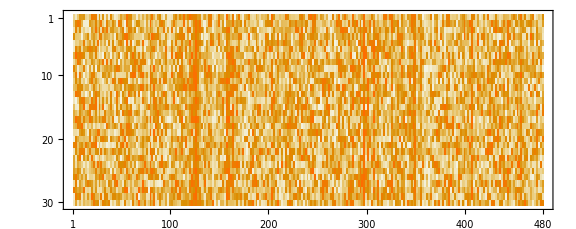

```mathematica
(anomalData = Transpose[Map[Drop[#,20]&,#["Values"]&/@Values[anomalTs],{1}]])//(MatrixPlot[Transpose[#],ImageSize->Large]&
```

Here are the correlations between the values

```mathematica
Round[Correlation[anomalData],.01]//MatrixForm
```

(1. | 0.26 | 0.17 | 0.3 | 0.32 | 0.18 | 0.25 | 0.13 | 0.17 | 0.17 | 0.22 | 0.2 | 0.14 | 0.27 | 0.19 | 0.17 | 0.23 | 0.13 | 0.19 | 0.11 | 0.19 | 0.11 | 0.28 | 0.07 | 0.25 | 0.17 | 0.07 | 0.43 | 0.26 | 0.12
0.26 | 1. | 0.21 | 0.18 | 0.24 | 0.15 | 0.2 | 0.11 | 0.15 | 0.12 | 0.25 | 0.19 | 0.15 | 0.23 | 0.13 | 0.05 | 0.24 | 0.26 | 0.13 | 0.14 | 0.19 | 0.15 | 0.18 | 0.07 | 0.3 | 0.17 | 0.07 | 0.34 | 0.31 | 0.06
0.17 | 0.21 | 1. | 0.11 | 0.21 | 0.12 | 0.28 | 0.11 | 0.12 | 0.14 | 0.11 | 0.09 | 0.24 | 0.19 | 0.09 | 0.09 | 0.32 | 0.12 | 0.1 | 0.11 | 0.07 | 0.03 | 0.14 | 0.1 | 0.32 | 0.1 | 0.1 | 0.26 | 0.08 | 0.06
0.3 | 0.18 | 0.11 | 1. | 0.23 | 0.12 | 0.15 | -0.01 | 0.06 | 0.06 | 0.19 | 0.17 | 0.1 | 0.14 | 0.08 | 0.08 | 0.15 | 0.06 | 0.12 | 0.03 | 0.11 | 0.11 | 0.27 | 0.05 | 0.19 | 0.1 | 0.11 | 0.34 | 0.16 | 0.03
0.32 | 0.24 | 0.21 | 0.23 | 1. | 0.2 | 0.19 | 0.1 | 0.1 | 0.13 | 0.26 | 0.22 | 0.14 | 0.18 | 0.05 | 0.09 | 0.17 | 0.13 | 0.12 | 0.11 | 0.09 | 0.15 | 0.27 | 0.12 | 0.25 | 0.04 | 0.11 | 0.4 | 0.19 | 0.14
0.18 | 0.15 | 0.12 | 0.12 | 0.2 | 1. | 0.21 | 0.01 | 0.07 | 0.47 | 0.2 | 0.15 | 0.16 | 0.09 | 0.08 | 0.16 | 0.22 | 0.09 | 0.12 | 0.06 | 0.17 | 0.12 | 0.16 | 0.11 | 0.19 | 0.12 | 0.1 | 0.23 | 0.18 | 0.13
0.25 | 0.2 | 0.28 | 0.15 | 0.19 | 0.21 | 1. | 0.09 | 0.14 | 0.2 | 0.16 | 0.2 | 0.22 | 0.22 | 0.11 | 0.21 | 0.39 | 0.15 | 0.17 | 0.05 | 0.12 | 0.14 | 0.22 | 0.07 | 0.33 | 0.19 | 0.23 | 0.4 | 0.21 | 0.05
0.13 | 0.11 | 0.11 | -0.01 | 0.1 | 0.01 | 0.09 | 1. | 0.07 | 0.13 | 0.05 | 0.04 | 0.08 | 0.12 | 0.1 | 0.08 | 0.09 | 0.13 | 0.09 | 0.23 | 0.08 | 0. | 0.1 | 0.19 | 0.12 | 0.14 | 0.11 | 0.1 | 0.11 | 0.08
0.17 | 0.15 | 0.12 | 0.06 | 0.1 | 0.07 | 0.14 | 0.07 | 1. | 0.18 | 0.12 | 0.22 | 0.11 | 0.18 | 0.11 | 0.19 | 0.13 | 0.1 | 0.19 | 0.06 | 0.13 | 0.13 | 0.13 | 0.08 | 0.17 | 0.18 | 0.09 | 0.21 | 0.15 | 0.12
0.17 | 0.12 | 0.14 | 0.06 | 0.13 | 0.47 | 0.2 | 0.13 | 0.18 | 1. | 0.24 | 0.2 | 0.13 | 0.11 | 0.07 | 0.14 | 0.11 | 0.09 | 0.2 | 0.08 | 0.16 | 0.07 | 0.19 | 0.18 | 0.23 | 0.1 | 0.13 | 0.27 | 0.2 | 0.16
0.22 | 0.25 | 0.11 | 0.19 | 0.26 | 0.2 | 0.16 | 0.05 | 0.12 | 0.24 | 1. | 0.13 | 0.13 | 0.26 | 0.09 | 0.07 | 0.11 | 0.16 | 0.09 | 0.02 | 0.17 | 0.18 | 0.16 | 0.09 | 0.17 | 0.1 | 0.13 | 0.38 | 0.5 | 0.1
0.2 | 0.19 | 0.09 | 0.17 | 0.22 | 0.15 | 0.2 | 0.04 | 0.22 | 0.2 | 0.13 | 1. | 0.13 | 0.21 | 0.11 | 0.09 | 0.15 | 0.22 | 0.03 | 0.09 | 0.17 | 0.13 | 0.2 | 0.08 | 0.26 | 0.13 | 0.21 | 0.34 | 0.16 | 0.08
0.14 | 0.15 | 0.24 | 0.1 | 0.14 | 0.16 | 0.22 | 0.08 | 0.11 | 0.13 | 0.13 | 0.13 | 1. | 0.19 | 0.14 | 0.16 | 0.21 | 0.11 | 0.23 | 0.13 | 0.11 | 0.11 | 0.11 | 0.08 | 0.17 | 0.08 | 0.07 | 0.21 | 0.16 | 0.04
0.27 | 0.23 | 0.19 | 0.14 | 0.18 | 0.09 | 0.22 | 0.12 | 0.18 | 0.11 | 0.26 | 0.21 | 0.19 | 1. | 0.2 | 0.19 | 0.18 | 0.14 | 0.11 | 0.14 | 0.3 | 0.09 | 0.23 | 0.09 | 0.2 | 0.17 | 0.09 | 0.41 | 0.27 | 0.08
0.19 | 0.13 | 0.09 | 0.08 | 0.05 | 0.08 | 0.11 | 0.1 | 0.11 | 0.07 | 0.09 | 0.11 | 0.14 | 0.2 | 1. | 0.2 | 0.12 | 0.13 | 0.2 | 0.11 | 0.18 | 0.13 | 0.18 | 0.11 | 0.1 | 0.1 | 0.11 | 0.16 | 0.1 | 0.07
0.17 | 0.05 | 0.09 | 0.08 | 0.09 | 0.16 | 0.21 | 0.08 | 0.19 | 0.14 | 0.07 | 0.09 | 0.16 | 0.19 | 0.2 | 1. | 0.15 | 0.11 | 0.3 | 0.13 | 0.12 | 0.19 | 0.08 | 0.06 | 0.04 | 0.19 | 0.11 | 0.15 | 0.06 | 0.01
0.23 | 0.24 | 0.32 | 0.15 | 0.17 | 0.22 | 0.39 | 0.09 | 0.13 | 0.11 | 0.11 | 0.15 | 0.21 | 0.18 | 0.12 | 0.15 | 1. | 0.18 | 0.18 | 0.04 | 0.08 | 0.2 | 0.19 | 0.08 | 0.45 | 0.19 | 0.11 | 0.33 | 0.19 | 0.1
0.13 | 0.26 | 0.12 | 0.06 | 0.13 | 0.09 | 0.15 | 0.13 | 0.1 | 0.09 | 0.16 | 0.22 | 0.11 | 0.14 | 0.13 | 0.11 | 0.18 | 1. | 0.03 | 0.11 | 0.1 | 0.1 | 0.09 | 0.14 | 0.19 | 0.14 | 0.13 | 0.22 | 0.14 | -0.01
0.19 | 0.13 | 0.1 | 0.12 | 0.12 | 0.12 | 0.17 | 0.09 | 0.19 | 0.2 | 0.09 | 0.03 | 0.23 | 0.11 | 0.2 | 0.3 | 0.18 | 0.03 | 1. | 0.06 | 0.21 | 0.18 | 0.09 | 0.16 | 0.15 | 0.12 | 0.04 | 0.16 | 0.07 | 0.1
0.11 | 0.14 | 0.11 | 0.03 | 0.11 | 0.06 | 0.05 | 0.23 | 0.06 | 0.08 | 0.02 | 0.09 | 0.13 | 0.14 | 0.11 | 0.13 | 0.04 | 0.11 | 0.06 | 1. | 0.12 | 0.09 | 0.1 | 0.15 | 0.07 | 0.14 | 0.11 | 0.13 | 0.06 | 0.14
0.19 | 0.19 | 0.07 | 0.11 | 0.09 | 0.17 | 0.12 | 0.08 | 0.13 | 0.16 | 0.17 | 0.17 | 0.11 | 0.3 | 0.18 | 0.12 | 0.08 | 0.1 | 0.21 | 0.12 | 1. | 0.12 | 0.16 | 0.12 | 0.08 | 0.14 | 0.2 | 0.26 | 0.21 | 0.12
0.11 | 0.15 | 0.03 | 0.11 | 0.15 | 0.12 | 0.14 | 0. | 0.13 | 0.07 | 0.18 | 0.13 | 0.11 | 0.09 | 0.13 | 0.19 | 0.2 | 0.1 | 0.18 | 0.09 | 0.12 | 1. | 0.15 | 0.05 | 0.17 | 0.13 | 0.11 | 0.19 | 0.16 | 0.11
0.28 | 0.18 | 0.14 | 0.27 | 0.27 | 0.16 | 0.22 | 0.1 | 0.13 | 0.19 | 0.16 | 0.2 | 0.11 | 0.23 | 0.18 | 0.08 | 0.19 | 0.09 | 0.09 | 0.1 | 0.16 | 0.15 | 1. | 0.19 | 0.21 | 0.1 | 0.13 | 0.34 | 0.16 | 0.14
0.07 | 0.07 | 0.1 | 0.05 | 0.12 | 0.11 | 0.07 | 0.19 | 0.08 | 0.18 | 0.09 | 0.08 | 0.08 | 0.09 | 0.11 | 0.06 | 0.08 | 0.14 | 0.16 | 0.15 | 0.12 | 0.05 | 0.19 | 1. | 0.14 | 0.06 | 0.08 | 0.2 | 0.08 | 0.13
0.25 | 0.3 | 0.32 | 0.19 | 0.25 | 0.19 | 0.33 | 0.12 | 0.17 | 0.23 | 0.17 | 0.26 | 0.17 | 0.2 | 0.1 | 0.04 | 0.45 | 0.19 | 0.15 | 0.07 | 0.08 | 0.17 | 0.21 | 0.14 | 1. | 0.07 | 0.13 | 0.4 | 0.17 | 0.16
0.17 | 0.17 | 0.1 | 0.1 | 0.04 | 0.12 | 0.19 | 0.14 | 0.18 | 0.1 | 0.1 | 0.13 | 0.08 | 0.17 | 0.1 | 0.19 | 0.19 | 0.14 | 0.12 | 0.14 | 0.14 | 0.13 | 0.1 | 0.06 | 0.07 | 1. | 0.18 | 0.23 | 0.08 | 0.04
0.07 | 0.07 | 0.1 | 0.11 | 0.11 | 0.1 | 0.23 | 0.11 | 0.09 | 0.13 | 0.13 | 0.21 | 0.07 | 0.09 | 0.11 | 0.11 | 0.11 | 0.13 | 0.04 | 0.11 | 0.2 | 0.11 | 0.13 | 0.08 | 0.13 | 0.18 | 1. | 0.22 | 0.1 | 0.07
0.43 | 0.34 | 0.26 | 0.34 | 0.4 | 0.23 | 0.4 | 0.1 | 0.21 | 0.27 | 0.38 | 0.34 | 0.21 | 0.41 | 0.16 | 0.15 | 0.33 | 0.22 | 0.16 | 0.13 | 0.26 | 0.19 | 0.34 | 0.2 | 0.4 | 0.23 | 0.22 | 1. | 0.34 | 0.18
0.26 | 0.31 | 0.08 | 0.16 | 0.19 | 0.18 | 0.21 | 0.11 | 0.15 | 0.2 | 0.5 | 0.16 | 0.16 | 0.27 | 0.1 | 0.06 | 0.19 | 0.14 | 0.07 | 0.06 | 0.21 | 0.16 | 0.16 | 0.08 | 0.17 | 0.08 | 0.1 | 0.34 | 1. | 0.04
0.12 | 0.06 | 0.06 | 0.03 | 0.14 | 0.13 | 0.05 | 0.08 | 0.12 | 0.16 | 0.1 | 0.08 | 0.04 | 0.08 | 0.07 | 0.01 | 0.1 | -0.01 | 0.1 | 0.14 | 0.12 | 0.11 | 0.14 | 0.13 | 0.16 | 0.04 | 0.07 | 0.18 | 0.04 | 1.)

Let us extract the return data and define anomaly as areas wherein the anomaly score is higher than 0.5

```mathematica
(retsData = Transpose[Map[Drop[#,20]&,#["Values"]&/@Values[stockTs],{1}]]);
```

```mathematica
Binarize[Image[Transpose[anomalData]],.5]
```

-Graphics-

Let us count the number of anomalous stocks within a day:

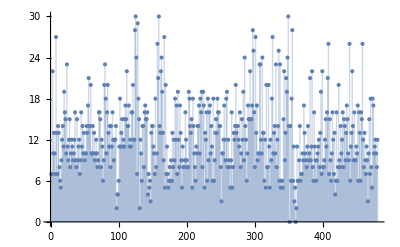

```mathematica
(anomalCounts = Count[#,_?(#>.5&)]&/@anomalData)//ListPlot[#,Filling->Axis]&
```

Here are the positions  with≥20 stocks anomalous per day

```mathematica
posGreater20 = Position[anomalCounts,_?(#≥20&)]//Flatten
```

{3,8,24,56,59,79,80,84,112,121,124,125,126,128,157,158,159,162,163,167,169,272,285,293,297,298,301,307,308,311,317,320,326,331,335,337,343,346,348,349,355,381,384,399,407,408,423,439,443,458}

Here are the positions of values ≤10 stocks anomalous per day

```mathematica
posLess10 = Position[anomalCounts,_?(#≤10&)]//Flatten
```

{1,2,4,6,7,10,13,14,15,16,23,26,29,30,33,34,37,38,40,43,44,48,50,51,52,60,61,63,65,66,68,69,70,74,77,78,82,88,93,97,98,99,100,127,131,133,134,137,143,144,145,146,147,152,153,155,156,166,168,170,172,173,174,175,176,177,178,180,182,186,189,192,193,195,196,197,200,201,202,208,211,212,213,215,219,223,226,230,232,235,238,240,241,250,251,252,253,257,260,262,263,264,265,267,268,279,280,284,288,289,300,304,305,306,310,314,316,318,319,322,324,327,330,332,336,338,339,340,341,344,351,353,356,358,359,360,361,363,364,365,367,368,369,370,371,374,375,376,379,380,382,385,386,389,390,391,392,395,398,400,401,402,409,411,412,413,416,418,419,421,422,424,425,427,430,433,437,438,440,445,447,448,450,452,455,460,462,463,465,466,467,469,471,472,475,478,479}

Let us visualize these selected points

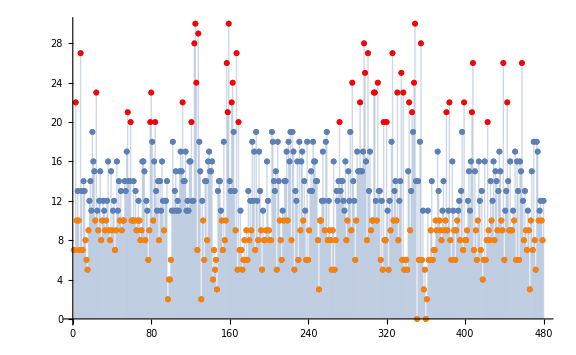

```mathematica
ListPlot[Style[#,If[#≥20,Red,If[#≤10,Orange]]]&/@anomalCounts,Filling->Axis,ImageSize->Large]
```

Now let us examine the average returns over these selected intervals

Here is the average over the returns over those with ≥20 stocks with P(anomaly)≥.5

```mathematica
Mean[Mean[retsData⟦posGreater20⟧]]
```

-0.353727 %

Here is the average over the returns over those with ≤10 stocks with P(anomaly)≥.5

```mathematica
Mean[Mean[retsData⟦posLess10⟧]]
```

0.126727 %

Here is the same analysis with just the Dow Jones:

```mathematica
dow = Drop[stockTs[Entity["Financial","^DJI"]]["Values"],20];
```

Here is the average over the Dow over those with ≥20 stocks with P(anomaly)≥.5

```mathematica
Mean[dow⟦posGreater20⟧]
```

-0.370067 %

Here is the average over the Dow over those with ≤10 stocks with P(anomaly)≥.5

```mathematica
Mean[dow⟦posLess10⟧]
```

0.110058 %

Notice the relative uniformity in the probability of anomaly counts.

```mathematica
Manipulate[Histogram[anomalTs[entity]["Values"],],{entity,FEOI},SaveDefinitions->True]
```

What this means that when more than 20/30stocks are anomalous ( P(anomaly)≥.5 ), it turns out that those days the Dow Jones is down, while when there are less than 10/30stocks . This hints at a systemic origin of anomaly as when anomalies occur together the stock market is generally down even though, individually, the probability of anomaly is relatively uniform.

#### Examining Anomaly Probability Together

Let’s input more points by using all 30 stocks and putting that through anomaly detection

```mathematica
tsw2anomalProbMultiDim[ts_]:=
Module[{tr,an},
{tr,an} = TakeDrop[ts,Length[ts]-1];
RarerProbability[LearnDistribution[tr//Flatten,Method->"KernelDensityEstimation",TrainingProgressReporting->"SimplePanel"],an//Flatten]
]
```

```mathematica
anomalTogether = tsw2anomalProbMultiDim/@Partition[Transpose[Normal[#["Values"]]&/@Values[stockTs]], windowSize,1]
```

{{0.60143,0.353692,0.756643,0.390142,0.46734,0.496015,0.667275,0.335354,0.634215,0.562904,0.511245,0.419301,0.698773,0.669561,0.754201,0.373703,0.438985,0.684107,0.187362,0.617827,0.328954,0.632486,0.797023,0.569777,0.738058,0.480739,0.335966,0.560298,0.337581,0.902446},478,{0.583639,0.100405,0.449452,0.641936,0.941005,0.654601,0.821074,0.902865,0.718481,0.917222,0.435025,0.549799,0.481427,0.239807,0.624755,0.191288,0.806164,0.293592,0.126191,0.487028,0.709387,0.196968,0.266411,0.609051,0.705849,0.456123,0.939092,0.620846,0.708854,0.480922}}
 |  |  |  |

Here are pre-computed values

```mathematica
anomalTogether=
```

Here is the probability distribution for four anomaly timeseries from the systemic anomaly.

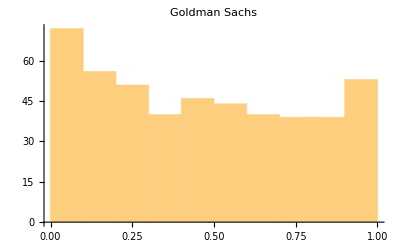
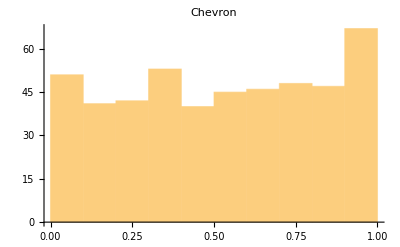
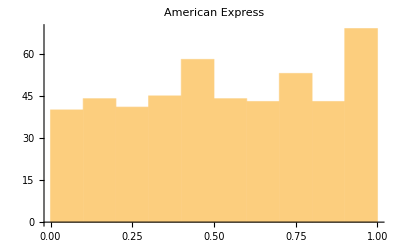
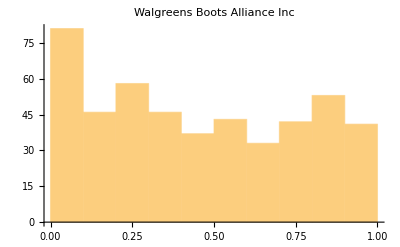

```mathematica
RandomSample[MapThread[Histogram[#,PlotLabel->#2]&,{Transpose[anomalTogether],FEOI}],4]
```

Notice here that returns are relatively correlated, while the individual anomalies are all rather independent. However, on the systemic anomalies, the index (Dow Jones, first row/column) anomalies appear to be highly correlated with the anomalies of each the individual components, indicating a systemic but non-pairwise risk.

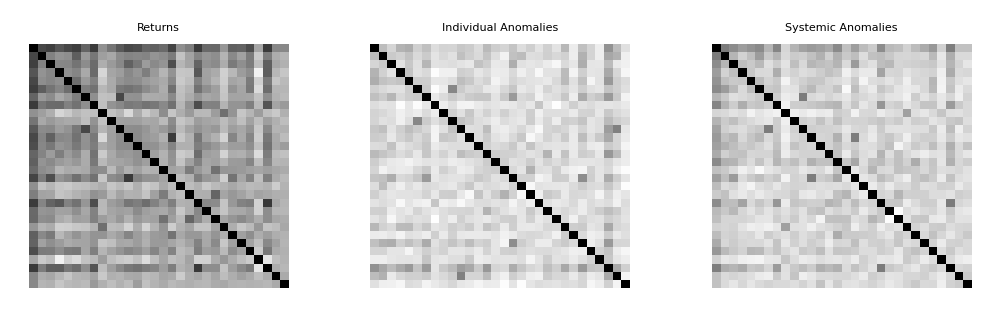
-Graphics-Correlation Matrices

```mathematica
dat2 = Transpose[Drop[Normal[#["Values"]],20]&/@Values[anomalTs]];
dat = Normal[#["Values"]]&/@Values[stockTs];
Labeled[GraphicsRow[{ArrayPlot[Correlation[Transpose[dat]],PlotLabel-> Style["Returns",Bold,20]],
		   ArrayPlot[Correlation[dat2],PlotLabel->Style["Individual Anomalies",Bold,20]],
		      ArrayPlot[Correlation[anomalTogether],PlotLabel->Style["Systemic Anomalies",Bold,20]]},
			ImageSize->1000],Style["Correlation Matrices",Bold,36,FontFamily->"Sans"],Top]
```

### Examining Anomaly and Return

Let us examine the relation between anomalies and the return on stocks

Here is a scatter plot of the probability of anomaly against the return values. Note the increase in skedasticity as anomaly probability increases

```mathematica
Manipulate[ListPlot[Transpose[{Take[anomalTs[entity]["Values"],-500],Take[stockTs[entity]["Values"],-500]}],],{entity,FEOI},SaveDefinitions->True]
```

Here is a scatter plot of the average returns across the stocks to the anomaly probability (the ones to the far right are from the padding)

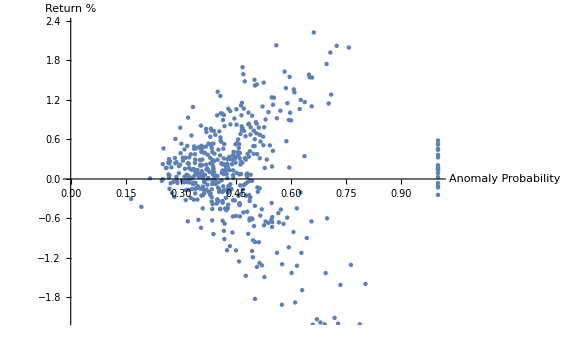

```mathematica
ListPlot[Transpose[{Take[Mean[anomalTs]["Values"],-500],Take[Mean[stockTs]["Values"],-500]}],]
```

Let’s compare this to the relation between this and the next day...

#### Comparison next day (baseline comparison)

Here is a scatter plot of the prior day probability of anomaly against the return values. Note that there is no relation between the two variables.

```mathematica
Manipulate[ListPlot[Transpose[{Take[Take[anomalTs[entity]["Values"],-500],499],Take[stockTs[entity]["Values"],-499]}],],{{entity,Entity["Financial","NYSE:MMM"]},FEOI},SaveDefinitions->True]
```

Here is a scatter plot of the average returns across the stocks to the prior day anomaly probability (the ones to the far right are from the padding)

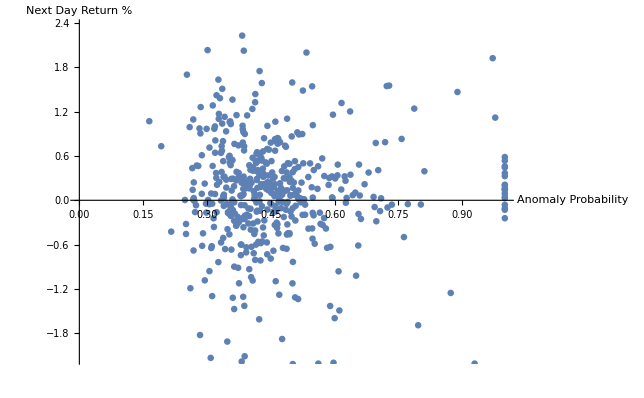

```mathematica
ListPlot[Transpose[{Take[Take[Mean[anomalTs]["Values"],-500],499],Take[Mean[stockTs]["Values"],-499]}],]
```

The conclusion here is that there is essentially no relation between prior day anomaly and next-day future returns, indicating the prior behaviour was not coincidental and that anomalies are relatively quick and not long term.

### 20 Day Prior-σ and Anomaly Probability

Here is a function which converts a time series to a time series of  standard deviations of points n days prior to a given point in the timeseries

```mathematica
ts2StDev[ts_,window_]:=
   Module[{out},
     out = StandardDeviation/@Partition[ts["Values"],window,1];
     TimeSeries[Transpose[{ts["Dates"],PadLeft[out,ts["PathLength"]]}]]
   ]
```

```mathematica
Manipulate[
σTs = ts2StDev[stockTs[entity],lookback];
Column[{ListPlot[Transpose[{Take[anomalTs[entity]["Values"],-500],Take[σTs["Values"],-500]}],],
      DateListPlot[σTs,]}],
         {entity,FEOI},{{lookback,20},1,30,1},SaveDefinitions->True]
```

This indicates that anomaly is not simply the product of volatility.

### A Weighted Portfolio

In this section the effect on returns of creating a weighted portfolio based on anomaly probability will be examined.

Let us first define a simple normalization function which converts the probabilities of anomaly into a series of weights for the portfolio

```mathematica
sum2one[a_List] := a/Total[a]
```

Extract the returns and place them into a matrix

```mathematica
rets = Transpose[Normal[#["Values"]]&/@Values[KeyDrop[stockTs,{Entity["Financial","^DJI"]}]]]//N;
```

Extract the anomaly probabilities, normalize them, and place them into a matrix

```mathematica
anomp = sum2one/@Transpose[Normal[#["Values"]]&/@Values[KeyDrop[anomalTs,{Entity["Financial","^DJI"]}]]]//N;
```

Taking the dot product between the returns and anomalies at each time step yields the weighted return time-series based on anomaly probability

```mathematica
myRetsNum = Table[anomp⟦x⟧.rets⟦x⟧,{x,Length[anomp]}];
myRetsTs = TimeSeries[Transpose[{stockTs[Entity["Financial","NYSE:MMM"]]["Dates"],myRetsNum}]]
```

TimeSeries[…]

Surprisingly, the return values are quite similar to the Dow Jones

```mathematica
Manipulate[DateListPlot[{stockTs[entity]/Quantity[100, "Percent"],myRetsTs},],{{entity,Entity["Financial","^DJI"]},FEOI},SaveDefinitions->True]
```

```mathematica
Manipulate[
lm=LinearModelFit[Transpose[{stockTs[entity]["Values"],myRetsTs["Values"]}],β,β,IncludeConstantBasis->False];
ListPlot[Transpose[{myRetsTs["Values"],stockTs[entity]["Values"]}],
				    PlotLabel->(ToString[lm["BestFit"]]<>"\nCorrelation:"Correlation[myRetsTs,stockTs[entity]]),
				    AxesLabel->{"Portfolio\n Returns",entity["Name"]<>" Returns"},
                                         ImageSize->Large
],{{entity,Entity["Financial","^DJI"]},FEOI},SaveDefinitions->True]
```

### Offset by One Day Weighted Portfolio

As a comparison, the portfolio which is offset by one day is also examined

Repeat the process from the previous section, but with offset values

```mathematica
Orets = Drop[rets,1];
Oanomp = Drop[anomp,1];
OmyRetsNum = Table[Oanomp⟦x⟧.Orets⟦x⟧,{x,Length[Oanomp]}];
OmyRetsTs = TimeSeries[Transpose[{Rest[stockTs[Entity["Financial","NYSE:MMM"]]["Dates"]],OmyRetsNum}]]
```

TimeSeries[…]

Interestingly these values are also similar to the DJI

```mathematica
Manipulate[DateListPlot[{stockTs[entity]/Quantity[100, "Percent"],OmyRetsTs},],{entity,FEOI},SaveDefinitions->True]
```

```mathematica
Manipulate[
dat = Rest[stockTs[entity]["Values"]];
lm=LinearModelFit[Transpose[{dat,OmyRetsTs["Values"]}],β,β,IncludeConstantBasis->False];
ListPlot[Transpose[{OmyRetsTs["Values"],dat}],
				    PlotLabel->(ToString[lm["BestFit"]]<>"\nCorrelation:"Correlation[myRetsTs,stockTs[entity]]),
				    AxesLabel->{"Yesterday\nPortfolio\n Returns",entity["Name"]<>" Returns"},
                                         ImageSize->Large
],{{entity,Entity["Financial","^DJI"]},FEOI},SaveDefinitions->True]
```

Notice how similar all these average values are to 1/30 for each of the 30 components . This indicates that the weights in the portfolio are are all about average

```mathematica
1/30//N
```

0.0333333

```mathematica
Mean[anomp]
```

{0.032809,0.0347204,0.0342334,0.034859,0.0335579,0.0330868,0.0337829,0.0359465,0.0340958,0.0365247,0.0342626,0.0350461,0.033859,0.0335339,0.0354648,0.0361261,0.0332769,0.0346115,0.0343056,0.0349231,0.0339462,0.0364756,0.033643,0.0344879,0.0339536,0.0341202,0.0344023,0.035506,0.0344392}

```mathematica
Mean[Oanomp]
```

{0.0328056,0.0347208,0.0342329,0.0348598,0.033556,0.033084,0.0337814,0.0359494,0.034095,0.0365288,0.0342622,0.0350472,0.0338578,0.033532,0.0354668,0.0361294,0.0332745,0.0346117,0.0343052,0.034924,0.0339451,0.0364796,0.0336413,0.0344879,0.0339526,0.0341195,0.0344021,0.035508,0.0344391}

## Section V: Future Work

In the future, I aim to refine the stock pricing anomaly conversion model and perform further analysis with the anomaly signal. Problems with the non-deterministic nature of the routine must be addressed and more methods of anomaly detection should be explored. The fidelity of these methods should be examined with rigor. Further work on examining the notion of systemic anomaly should be performed to yield more insight into the nature of market anomaly. Other data sources may be incorporated (e.g. macroeconomic factors, recent events) to facilitate this task. More stocks may be examined beyond the Dow Jones. The anomaly signal itself may also be examined in further detail to took for patterns such as those of seasonality.